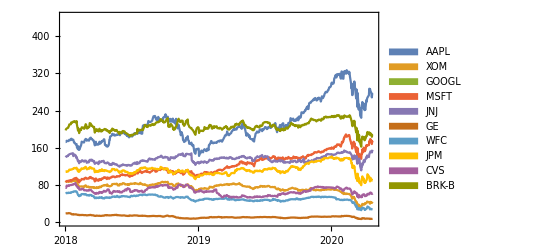

```mathematica
sp500const={"AAPL","XOM","GOOGL","MSFT","JNJ","GE","WFC","JPM","CVS","BRK-B"};
sp500ts=TimeSeries[FinancialData[#,"Close",{{2018,1,1},{2020,04,23}}]]&/@sp500const;
DateListPlot[sp500ts,PlotLegends->SwatchLegend[sp500const,LegendLayout->{"Column",2}]]
```

```mathematica
correl = crossCorrelation[sp500ts]
```

crossCorrelation[{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]}]

```mathematica
correl
```

crossCorrelation[{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]}]

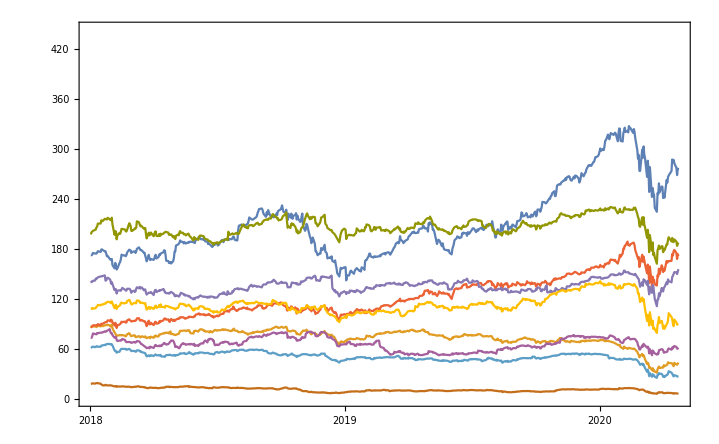

```mathematica
DateListPlot[correl[[1]]]
```